# w = w_0+w_a*z/(1+z)

```mathematica
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb];
```

## Constants

```mathematica
ompl=0.32; (*times apo x^2 *)
hcpl = 0.674;
H0pl=100*hcpl;
w0cpl =-1.06;
wacpl  = 0.2;
Gc = 6.674*10^(-11);
k1=3*H0pl^2/(8*Pi*Gc);
```

## W (z)

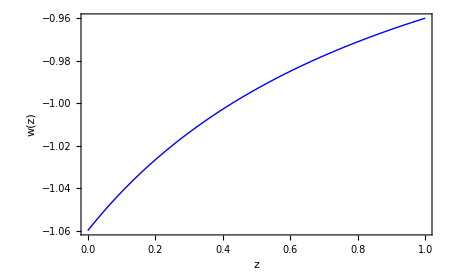

```mathematica
wz[z_,w0_?NumberQ,wa_?NumberQ] := w0+wa*(z/(1+z));
Plot[wz[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,Frame->True,FrameLabel->{"z","w(z)"},PlotStyle->{Blue,Thick},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large]]
```

## ρ_DE (z)

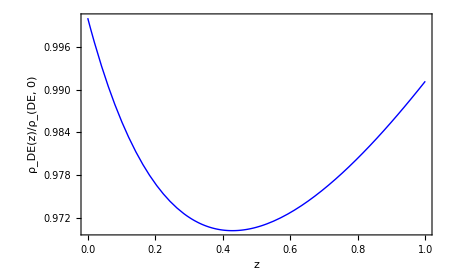

```mathematica
rde[z_,w0_,wa_]:= (1+z)^(3*(1+w0+wa))*Exp[-3*wa*z/(1+z)]
rde[z_,w0_,wa_];
Plot[rde[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",12},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z","ρ_DE(z)/ρ_(DE, 0)"},PlotStyle->{Blue,Thick}]
```

## V (z)

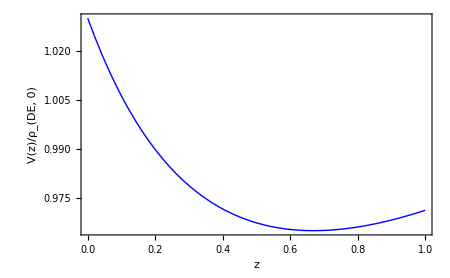

```mathematica
vz[z_,w0_,wa_]:=1/2*(1-w0-wa*z/(1+z))*(1+z)^(3*(1+w0+wa))*Exp[-3*wa*z/(1+z)]
vz[z_,w0_,wa_];
Plot[vz[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",12},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z","V(z)/ρ_(DE, 0)"},PlotStyle->{Blue,Thick}]
```

## H (z)

```mathematica
hzz[z_,w0_,wa_]:=H0pl*Sqrt[(ompl*(1+z)^3+(1-ompl)*(1+z)^(3*(1+w0+wa))*Exp[-3*wa*z/(1+z)])]
```

```mathematica
hzz[z,w0,wa];
```

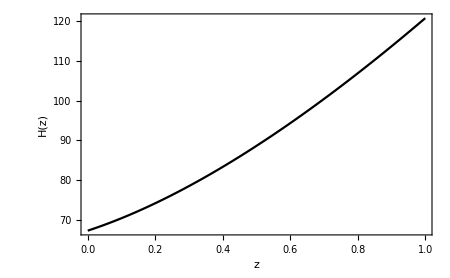

```mathematica
plcpl = Plot[hzz[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",12},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z","H(z)"},PlotStyle->{Black}]
```

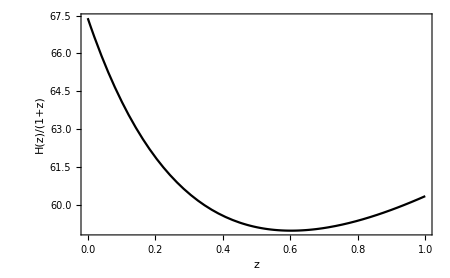

```mathematica
plcpl1 = Plot[hzz[z,w0cpl,wacpl]/(1+z),{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",12},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z","H(z)/(1+z)"},PlotStyle->{Black}]
```

## φ (z)

```mathematica
f1z[z_,w0_?NumberQ,wa_?NumberQ]:= Sqrt[Abs[1+w0+wa*z/(1+z)]]/((1+z)*Sqrt[1+ompl/(1-ompl)*(1+z)^(-3*(w0+wa))*Exp[3*wa*z/(1+z)]])
fzz[z_]:= NIntegrate[f1z[Z,w0cpl,wacpl],{Z,0,z}]
```

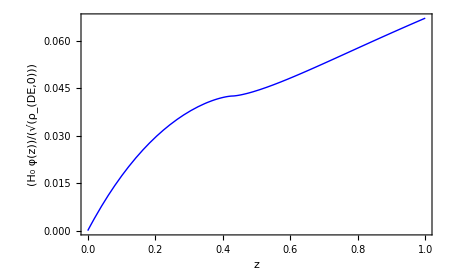

```mathematica
Plot[fzz[z],{z,0,1},ImageSize -> 450,PlotRange->{{0,1},Automatic},BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",(φ[z]*Subscript[H, 0])/(Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Blue,Thick}]
```

## V (φ)

```mathematica
(*ParametricPlot[{fzz[z],vz[z,-0.5,-0.3]},{z,0,1},PlotRange->Automatic]*)
points1=Table[{fzz[z],vz[z,w0cpl,wacpl]},{z,Range[0,1,0.001]}];//AbsoluteTiming
pl1=ListPlot[points1];
```

{166.752,Null}

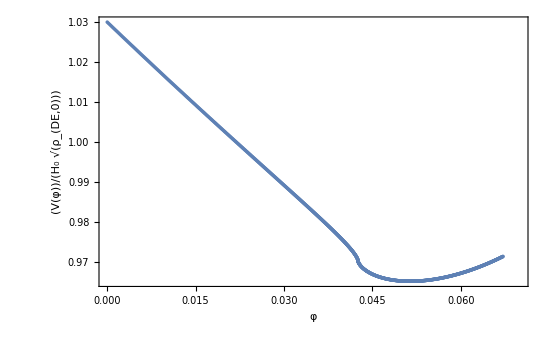

```mathematica
Show[pl1,ImageSize ->550,PlotRange->{{0,0.07},Automatic},BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"φ",V[φ]/(Subscript[H, 0]*Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Blue,Thick}]
```

## ΛCDM

```mathematica
ompl
H0pl
```

0.317

67.22

```mathematica
ompl=0.317; (*times apo x^2 *)
hlcdm = "0.672";
H0pl=100*hlcdm;
ompl
```

0.317

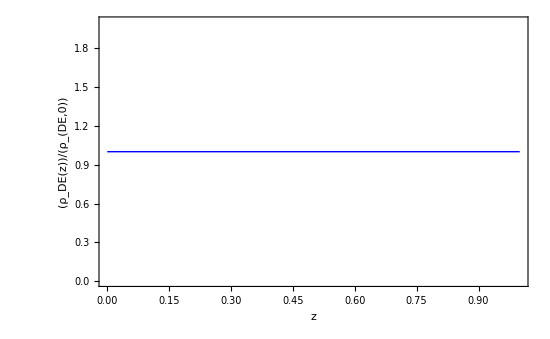

```mathematica
Plot[rde[z,-1,0],{z,0,1},ImageSize ->550,PlotRange->{{0,1},Automatic},BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",Subscript[ρ, DE][z]/Subscript[ρ, DE,0]},PlotStyle->{Blue,Thick}]
```

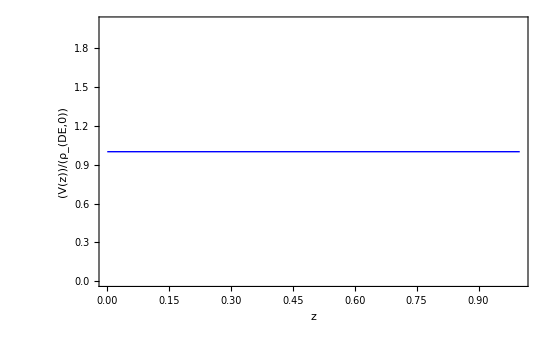

```mathematica
Plot[vz[z,-1,0],{z,0,1},ImageSize ->550,PlotRange->{{0,1},Automatic},BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",V[z]/Subscript[ρ, DE,0]},PlotStyle->{Blue,Thick}]
```

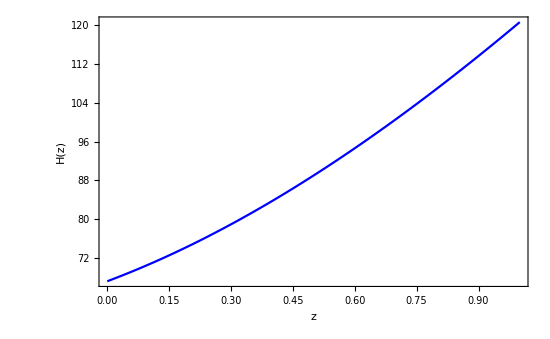

```mathematica
pll = Plot[hzz[z,-1,0],{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",H[z]},PlotStyle->{Blue}]
```

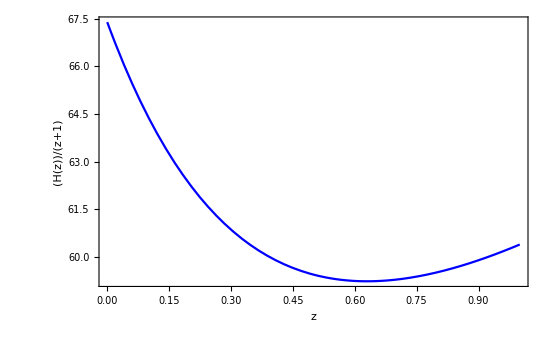

```mathematica
pll1 = Plot[hzz[z,-1,0]/(1+z),{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",H[z]/(1+z)},PlotStyle->{Blue}]
```

```mathematica
hzz[1,-1,0]//N
```

120.627

```mathematica
f1z[z,-1,0]
```

0

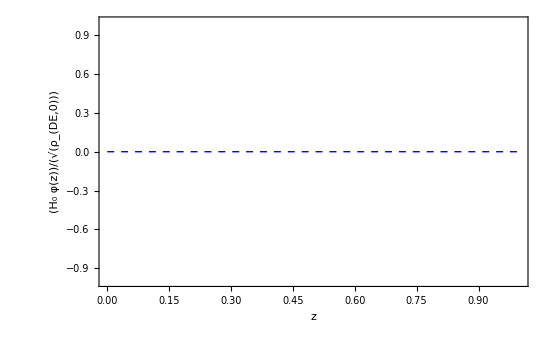

```mathematica
Plot[f1z[z,-1,0],{z,0,1},PlotRange->{{0,1},Automatic},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",(φ[z]*Subscript[H, 0])/(Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Blue,Dashed,Thick}]
```

```mathematica
Clear[ompl,H0pl]
```

## wCDM

```mathematica
ompl=0.316; (*times apo x^2 *)
hwcdm = "0.674";
H0pl=100*hwcdm;
w0wcdm = "-1.01";
```

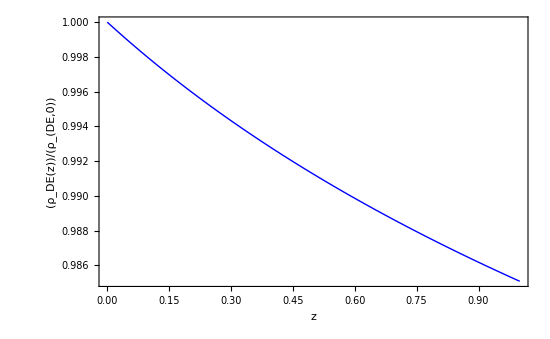

```mathematica
Plot[rde[z,w0wcdm,0],{z,0,1},PlotRange->{{0,1},Automatic},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",Subscript[ρ, DE][z]/Subscript[ρ, DE,0]},PlotStyle->{Blue,Thick}]
```

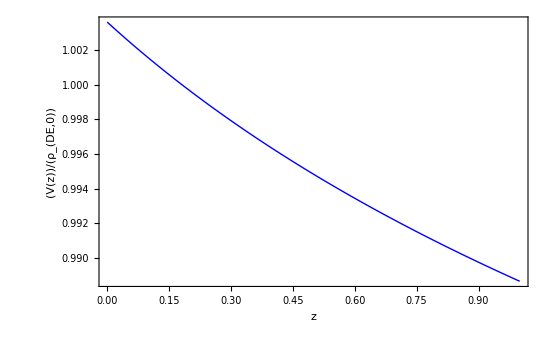

```mathematica
Plot[vz[z,w0wcdm,0],{z,0,1},ImageSize ->550,PlotRange->{{0,1},Automatic},BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",V[z]/Subscript[ρ, DE,0]},PlotStyle->{Blue,Thick}]
```

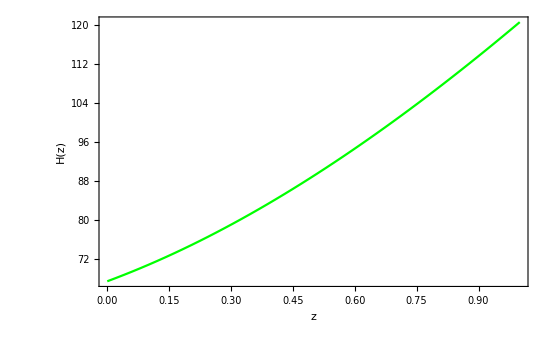

```mathematica
plw = Plot[hzz[z,w0wcdm,0],{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",H[z]},PlotStyle->{Green}]
```

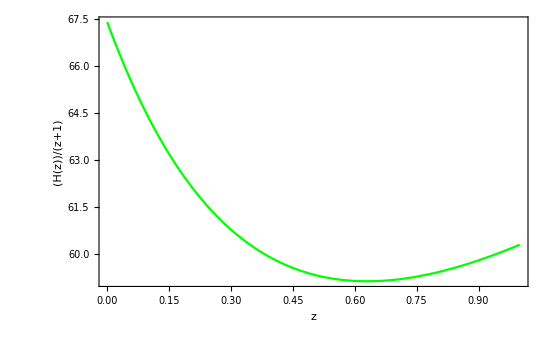

```mathematica
plw1 = Plot[hzz[z,w0wcdm,0]/(1+z),{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",H[z]/(1+z)},PlotStyle->{Green}]
```

```mathematica
f2z[z_,w0_?NumberQ,wa_?NumberQ]:= Sqrt[Abs[1+w0+wa*z/(1+z)]]/((1+z)*Sqrt[1+ompl/(1-ompl)*(1+z)^(-3*(w0+wa))*Exp[3*wa*z/(1+z)]])
f2z[Z,w0wcdm,0];
fzzz[z_]:= NIntegrate[f2z[Z,w0wcdm,0],{Z,0,z}]
```

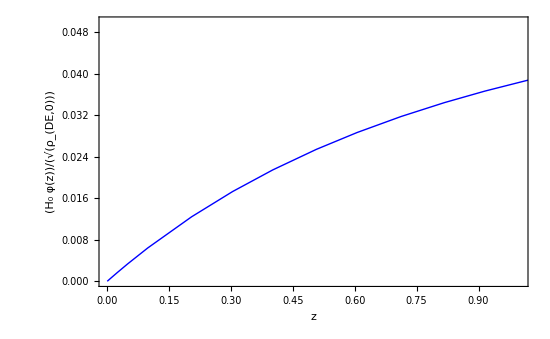

```mathematica
Plot[fzzz[z],{z,0,5},ImageSize ->550,PlotRange->{{0,1},{0,0.05}},BaseStyle->{Large,FontFamily->"Times",16},LabelStyle->Directive[Black,Large],Frame->True,FrameLabel->{"z",(φ[z]*Subscript[H, 0])/(Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Blue,Thick}]
```

```mathematica
NIntegrate[f2z[Z,w0wcdm,0],{Z,0,1}]
```

0.0384198

```mathematica
k123z[z_]:=Integrate[f2z[Z,w0wcdm,0],Z]
k123z[z]
```

-0.0562526 ArcTanh[1. √(1.+0.461988 (1.+Z)^3.02167)]

```mathematica
Plot[k123z[z],{z,-5,5}];
```

```mathematica
Plot[-0.056ArcTanh[1.0004*Sqrt[1+0.46*(1+z)^3]],{z,-5,6}];
```

```mathematica
l1234[Z_] :=  1. √(1.+0.46141997410363805 (1.+Z)^3.0216900000000004)
p1[z_] :=1/2*Log[(1+l123[z])/(1-l123[z])]
```

```mathematica
lnpl[Z_] := 1/2 Log[(1+1. √(1.+0.46141997410363805 (1.+Z)^3.0216900000000004))/(1-1. √(1.+0.46141997410363805 (1.+Z)^3.0216900000000004))]
Plot[Re[lnpl[z]],{z,-1,10}];
```

```mathematica
Plot[l1234[z],{z,-1,10}];
```

```mathematica
l1234[0.001]
```

1.20947

```mathematica
lnpl[1]
```

0.495997+1.5708 ⅈ

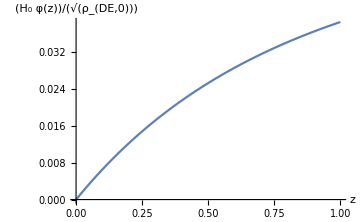

```mathematica
Plot[Re[fzzz[z]],{z,0,1},AxesLabel->{z,(φ[z]*Subscript[H, 0])/(Sqrt[Subscript[ρ, DE,0]])},LabelStyle->Directive[Black],ImageSize -> Medium,PlotRange->{{0,1},Automatic}]
```

```mathematica
Clear[ompl,H0pl,w0]
```

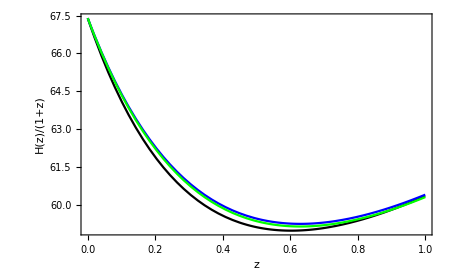

```mathematica
Show[plcpl1,pll1,plw1]
```

```mathematica
fzzz[50]
```

Re[NIntegrate[f2z[Z,-1.00723,0],{Z,0,50}]]

```mathematica
f2z[z,-1.00723,0]
```

0.0850294/((1+z) √(1+(ompl (1+z)^3.02169)/(1-ompl)))

```mathematica
0.08502940667792566/((1+z) √(1+0.46141997410363805 (1+z)^3.0216900000000004))
Plot[f2z[z],{z,0,1}]
```

0.0850294/((1+z) √(1+0.46142 (1+z)^3.02169))

-Graphics-